## New Boson - Excitation Energies

```mathematica
ClearAll["Global`*"]
```

```mathematica
exportPrePathMacMini="/Users/basavyr/Offline-Work/Repos/phdthesis/Chapters/Figures";
exportPrePathMacBook="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
exportPrePath="";
isSystemMacBook=ContainsAny[{"MacBook"},StringSplit[StringTemplate["``"][$MachineName],"-"]];
If[isSystemMacBook,exportPrePath=exportPrePathMacBook,exportPrePath=exportPrePathMacMini];
```

```mathematica
export[object_,name_]:=Export[StringTemplate["``/``.pdf"][exportPrePath,name],object, ImageResolution->1500];
```

```mathematica
A={1/(2*91),1/(2*9),1/(2*51)};
j=11/2;
I0=11/2;
thetarad=-119*π/180;
j1=j*Cos[thetarad];
j2=j*Sin[thetarad];
omega[I_]:=(((2I+1)(A[[2]]-A[[1]]-(A[[2]]*j2)/I)+2A[[1]]j1)*((2I+1)(A[[3]]-A[[1]])+2A[[1]]j1)-(A[[3]]-A[[1]])(A[[2]]-A[[1]]-(A[[2]]*j2)/I))^(1/2);
EnergyAbs[I_,n_]:=A[[1]] I^2-(2I+1)A[[1]]j1-I*A[[2]]*j2+omega[I]*(n+1/2)+A[[1]] j1^2+A[[2]] j2^2;
EnergyExc[I_,n_]:=EnergyAbs[I,n]-EnergyAbs[I0,0];
```

Experimental data

```mathematica
spins1=Table[i,{i,5.5,25.5,2}];
spins2=Table[i,{i,8.5,16.5,2}];
spins3=Table[i,{i,9.5,15.5,2}];
```

```mathematica
band1=Map[EnergyExc[#,0]&,spins1];
band2=Map[EnergyExc[#,0]&,spins2];
band3=Map[EnergyExc[#,1]&,spins3];
```

```mathematica
Print["B1\n",spins1,"\n",band1]
```

B1
{5.5,7.5,9.5,11.5,13.5,15.5,17.5,19.5,21.5,23.5,25.5}
{-4.71845×10^-16,0.771112,1.58354,2.43878,3.33737,4.27956,5.26546,6.29516,7.3687,8.4861,9.64739}

```mathematica
Print["B2\n",spins2,"\n",band2]
```

B2
{8.5,10.5,12.5,14.5,16.5}
{1.17203,2.00576,2.88264,3.80301,4.76704}

```mathematica
Print["B3\n",spins3,"\n",band3]
```

B3
{9.5,11.5,13.5,15.5}
{1.87842,2.79643,3.75657,4.75958}

Experimental data

```mathematica
gamma1Exp={372.9,659.8,854.3,999.7,1075.6,843.7,882.2,922.4,957.0,1005};
gamma2Exp={726.5,795.7,955.7,1111.7};
gamma3Exp={826.3,763.8,1009.0};
e01=358.0;
e02=1477.9;
e03=358.0+372.9+1197.1;
band1Exp={358.0,730.9,1390.7,2245.0,3244.7,4320.3,5164.0,6046.2,6968.6,7925.6,8930.6};
band2Exp={1477.9,2204.4,3000.1,3955.8,5067.5};
band3Exp={1928.0,2654.5,3450.2,4405.9,5517.6};
band1Exp=(#-e01)/1000&/@band1Exp;
band2Exp=(#-e01)/1000&/@band2Exp;
band3Exp=(#-e01)/1000&/@band3Exp;
```

```mathematica
f1=ListPlot[{Table[{spins1[[i]],EnergyExc[spins1[[i]],0]},{i,1,Length[spins1]}],Table[{spins1[[i]],band1Exp[[i]]},{i,1,Length[band1Exp]}]},Joined->{True,False},PlotStyle->{{Red,Thick},{Black}},AspectRatio->0.85,FrameStyle->Directive[Black,Thick]];
f2=ListPlot[Table[{spins2[[i]],EnergyExc[spins2[[i]],0]},{i,1,Length[spins2]}]];
f3=ListPlot[Table[{spins3[[i]],EnergyExc[spins3[[i]],0]},{i,1,Length[spins3]}]];
```

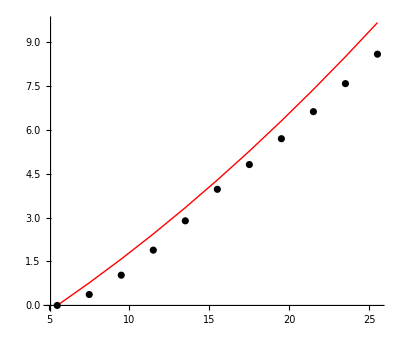

```mathematica
Show[f1]
```

```mathematica
› ›
```